{{4,1},{3,2},{3,3},{4,4}}

{4,0}7

{7,0}10

{10,0}14

{14,0}15

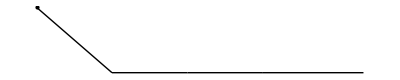

```mathematica
(*deklaracja zmiennych*)
Clear["Global`*"]
x:={4,3,3,4}
y:={1,2,3,4}
lista := {}
i:=1
position:=0
point={1,1};
start:=point
degree:=0
(* tworzenie listy par liczb całkowitych *)
While[i<=4,AppendTo[lista,{x[[i]], y[[i]]}];i++]
lista
startpoint:=Graphics[Point[point]]
lengths[5]=1;
For[i=1,i<5,i++,
(* dlugosc linii i rotacja *)
lengths[i]=lista[[i]][[1]];
rotations[i]=lista[[i]][[2]];
]
For[i=1,i<5,i++,
(* rysowanie linii *)
graph[i]=Graphics[Line[{start,{lengths[i],0}}]];
start={lengths[i],0};
lengths[i+1]+=start[[1]];
Print[start,lengths[i+1]]
]

Show[startpoint,graph[1],graph[2],graph[3],graph[4]]
```